The quantum phase estimation algorithm solves the problem of finding in the eigenvalue equation Uψ=ⅇ^ⅈ2πθ ψ, where is U a unitary operator. The inputs of the algorithm are qubits at the initial state 0^(⊗n), and the post-measurement state with largest probability is 2^n θ.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

The built-in circuit "PhaseEstimation" takes two input arguments: a unitary operator U and an integer n. For U, let's consider a phase operator.

For a phase operator with phase θ, find eigenvalues:

```mathematica
QuantumOperator[{"Phase",2 π θ}]["Eigenvalues"]
```

{1,ⅇ^(2 ⅈ π θ)}

The integer n specifies the number of qubits and controlled-U_j operators in the circuit, with j=0,1,…,n-1. The accuracy of phase estimation and the success probability depends on n (number of qubits):

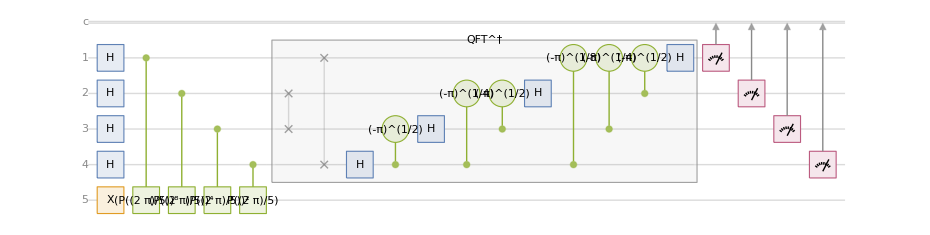

```mathematica
n=4;θ=1/5;
qc=QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator[{"Phase",2 π θ}],n}];
qc["Diagram",FontSize->11]
```

Return the corresponding measurement, with all qubits prepared in state:

```mathematica
mea=N@qc[]
```

QuantumMeasurement[…]

Plot corresponding probabilities:

```mathematica
mea["ProbabilityPlot"]
```

-Graphics-

Given the outcome with the largest probability, estimate the phase:

```mathematica
FromDigits[Keys[TakeLargest[mea["Probabilities"],1]][[1]]["Name"],2]/2^n//N
```

0.1875

As expected, it is a rough estimate (the expected value is θ=1/5=0.2), since a small value was chosen for n. If one increases n, with a higher probability, one can get a better estimate of the phase.

Estimate the phase (the expected value is 1/5=0.2) for n=6:

```mathematica
With[{m=N@QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator[{"Phase",2 Pi phase}],6}][]},FromDigits[Keys[TakeLargest[m["Probabilities"],1]][[1]]["Name"],2]/2^6//N]
```

0.203125